```mathematica
u=10;
hh=ArrayFlatten[Table[Which[i==j,ConstantArray[0,{2,2}],j==i-1,-ⅈ *J*Transpose[PauliMatrix[1]],j==i+1,ⅈ *J*PauliMatrix[1],Abs[i-j]>1,0],{i,1,u},{j,1,u}]];
```

```mathematica
MatrixForm[hh]
```

(0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0)

```mathematica
Eigenvalues[FullSimplify[ ⅈ PauliMatrix[1] ⅇ^(-ⅈ k) - ⅈ PauliMatrix[1] ⅇ^(ⅈ k)]]
```

{-2 Sin[k],2 Sin[k]}

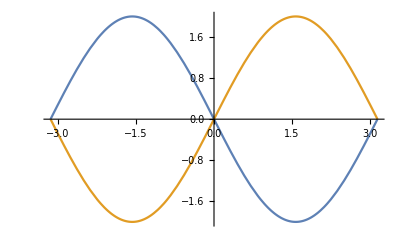

```mathematica
Plot[{-2 Sin[k],2 Sin[k]},{k,-π,π}]
```

```mathematica
FullSimplify[ ⅈ PauliMatrix[1] ⅇ^(-ⅈ Subscript[k, x]) - ⅈ PauliMatrix[1] ⅇ^(ⅈ Subscript[k, x])] + FullSimplify[ ⅈ PauliMatrix[2] ⅇ^(-ⅈ Subscript[k, y]) - ⅈ PauliMatrix[2] ⅇ^(ⅈ Subscript[k, y])]
```

{{0,2 Sin[k_x]-2 ⅈ Sin[k_y]},{2 Sin[k_x]+2 ⅈ Sin[k_y],0}}

```mathematica
Eigenvalues[{{0,2 Sin[Subscript[k, x]]-2 ⅈ Sin[Subscript[k, y]]},{2 Sin[Subscript[k, x]]+2 ⅈ Sin[Subscript[k, y]],0}}]
```

{-√2 √(2-Cos[2 k_x]-Cos[2 k_y]),√2 √(2-Cos[2 k_x]-Cos[2 k_y])}

```mathematica
hhh=ArrayFlatten[Table[Which[i==j,ConstantArray[0,{2,2}],j==i-1,-ⅈ *J*PauliMatrix[1],j==i+1,ⅈ *J*PauliMatrix[1],Mod[j-i,5]==0&&j-i>0, ⅈ*J*PauliMatrix[2],Mod[j-i,5]==0&&j-i<5,-ⅈ*J*PauliMatrix[2],Abs[i-j]>1&&j≠i+5&&j≠i-5,ConstantArray[0,{2,2}]],{i,1,25},{j,1,25}]];
```

```mathematica
MatrixForm[hhh]
```

(0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0
0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0
0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J
0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0
0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0
0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0
0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0
0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0
J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0
0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0
0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J
0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0 | ⅈ J | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | J | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ J | 0 | 0 | 0)